# Bounding scalar operator dimensions in 4D CFT

Defining the functions as defined in the references by Dolan Osborn.

```mathematica
k[β_,x_]:=x^(β/2)*Hypergeometric2F1[β/2,β/2,β,x];
```

```mathematica
g[Δ_,l_,z_,zb_]=((-0.5)^l)*(z*zb/(z-zb))*(k[Δ+l,z]*k[Δ-l-2,zb]-k[Δ+l,zb]*k[Δ-l-2,z]);
```

```mathematica
p[l_]:=2^(l+1)*(Factorial[l])^2/(Factorial[2l]);
```

```mathematica
u:=z*zb;
v:=(1-z)*(1-zb);
```

```mathematica
F[d_,Δ_,l_,z_,zb_]:=((((1-z)*(1-zb))^d )*(g[Δ,l,z,zb])-((z*zb)^d )*(g[Δ,l,1-z,1-zb]))/((z*zb)^d-((1-z)*(1-zb))^d)
```

Taking the limit where z and zb are identical.

```mathematica
Limit[F[1,l+2,l,z,zb],{z->zb}]
```

{1/(-2.+4. zb)(-0.5)^l (1.+l) (-1.+zb)^2 zb^2 (-2. (1.-1. zb)^l Hypergeometric2F1[1.+l,1.+l,2.+2. l,1.-1. zb]+2. zb^l Hypergeometric2F1[1.+l,1.+l,2.+2. l,zb]-1. (1.-1. zb)^l Hypergeometric2F1[2.+l,2.+l,3.+2. l,1.-1. zb]+(1.-1. zb)^l zb Hypergeometric2F1[2.+l,2.+l,3.+2. l,1.-1. zb]+zb^(1.+l) Hypergeometric2F1[2.+l,2.+l,3.+2. l,zb])}

```mathematica
PlotFunct[zb_,l_]:={1/(-2.+4. zb)(-0.5)^l (1.+l) (-1.+zb)^2 zb^2 (-2. (1.-1. zb)^l Hypergeometric2F1[1.+l,1.+l,2.+2. l,1.-1. zb]+2. zb^l Hypergeometric2F1[1.+l,1.+l,2.+2. l,zb]-1. (1.-1. zb)^l Hypergeometric2F1[2.+l,2.+l,3.+2. l,1.-1. zb]+(1.-1. zb)^l zb Hypergeometric2F1[2.+l,2.+l,3.+2. l,1.-1. zb]+zb^(1.+l) Hypergeometric2F1[2.+l,2.+l,3.+2. l,zb])}
```

Plot the function which shows all the F for various values of l and twist 2.

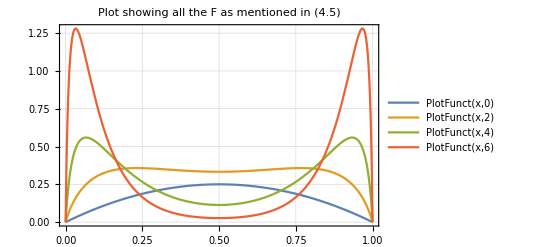

```mathematica
Plot[{PlotFunct[x,0],PlotFunct[x,2],PlotFunct[x,4],PlotFunct[x,6]},{x,0,1},PlotRange->Full,PlotTheme->"Detailed",PlotLabel->"Plot showing all the F as mentioned in (4.5)"]
```

```mathematica
SumFunct[x_,L_]:=Sum[p[l]*PlotFunct[x,l],{l,0,L,2}]
```

```mathematica
t=Table[SumFunct[x,L],{L,0,8,2}];
```

Plot the cumulative addition of the RHS of sum rule. This includes the p factor corresponding the primary.

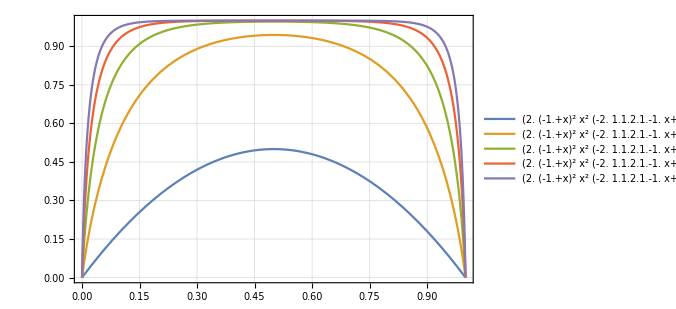

```mathematica
Plot[t,{x,0,1},PlotRange->Full,PlotTheme->"Detailed",PlotLabel->"",ImageSize->500]
```

This is the explicit form of the limit z=zb. Uncomment to get the said function.

```mathematica
%Limit[F[d,Δ,0,z,zb],{z->zb}];
ScalarPlot[d_,Δ_,zb_]:={-((1. (1. (1.-1. zb)^2 (zb^2)^d ((1/(-1.+zb)^2)0.25 (1.-1. zb)^Δ Δ Hypergeometric2F1[0.5 (-2.+Δ),0.5 (-2.+Δ),-2.+Δ,1.-1. zb] (-1. Hypergeometric2F1[1.+0.5 Δ,1.+0.5 Δ,1.+Δ,1.-1. zb]+zb Hypergeometric2F1[1.+0.5 Δ,1.+0.5 Δ,1.+Δ,1.-1. zb]-2. Hypergeometric2F1[0.5 Δ,0.5 Δ,Δ,1.-1. zb])-(1/(-1.+zb)^2)0.25 (1.-1. zb)^Δ (-2.+Δ) (-1. Hypergeometric2F1[1.+0.5 (-2.+Δ),1.+0.5 (-2.+Δ),-1.+Δ,1.-1. zb]+zb Hypergeometric2F1[1.+0.5 (-2.+Δ),1.+0.5 (-2.+Δ),-1.+Δ,1.-1. zb]-2. Hypergeometric2F1[0.5 (-2.+Δ),0.5 (-2.+Δ),-2.+Δ,1.-1. zb]) Hypergeometric2F1[0.5 Δ,0.5 Δ,Δ,1.-1. zb])+1. zb^2 (1.-2. zb+zb^2)^d (-0.25 zb^(-2.+Δ) (-2.+Δ) (zb Hypergeometric2F1[1.+0.5 (-2.+Δ),1.+0.5 (-2.+Δ),-1.+Δ,zb]+2. Hypergeometric2F1[0.5 (-2.+Δ),0.5 (-2.+Δ),-2.+Δ,zb]) Hypergeometric2F1[0.5 Δ,0.5 Δ,Δ,zb]+0.25 zb^(-2.+Δ) Δ Hypergeometric2F1[0.5 (-2.+Δ),0.5 (-2.+Δ),-2.+Δ,zb] (zb Hypergeometric2F1[1.+0.5 Δ,1.+0.5 Δ,1.+Δ,zb]+2. Hypergeometric2F1[0.5 Δ,0.5 Δ,Δ,zb]))))/(-1. (zb^2)^d+(1.-2. zb+zb^2)^d))}
```

For scalar field, we plot all the functions F while Δ increases.

```mathematica
ScalarTable=Table[ScalarPlot[1,Δ,x],{Δ,2,5,1}];
```

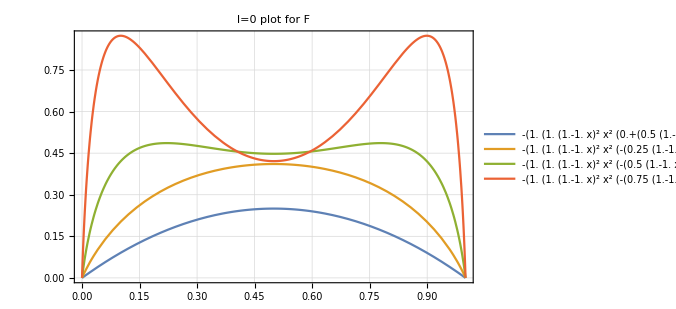

```mathematica
Plot[ScalarTable,{x,0,1},PlotRange->Full,PlotTheme->"Detailed",PlotLabel->"
l=0 plot for F ",ImageSize->500]
```

The graph showing that critical value for Δ is between 3.61 and 3.62 as the second derivative is changing sign.

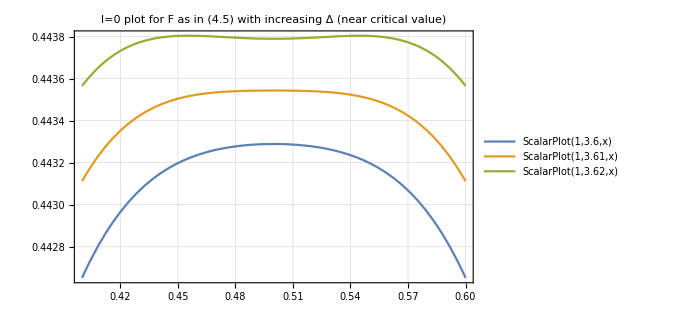

```mathematica
Plot[{ScalarPlot[1,3.6,x],ScalarPlot[1,3.61,x],ScalarPlot[1,3.62,x]},{x,0.4,0.6},PlotRange->Full,PlotTheme->"Detailed",PlotLabel->"
l=0 plot for F as in (4.5) with increasing Δ (near critical value)",ImageSize->500]
```

Uncomment this to get the most general function F for any l and Delta.

```mathematica
(*Limit[F[d,Δ,l,z,zb],{z->zb}];*)
```

```mathematica
SpinLPlot[d_,Δ_,l_,zb_]:={-(1/(-1. (zb^2)^d+(1.-2. zb+zb^2)^d))1. ((-0.5)^l (1.-1. zb)^2 (zb^2)^d (1/(-1.+zb)^2 0.25 (1.-1. zb)^Δ (2.+l-1. Δ) Hypergeometric2F1[0.5 (l+Δ),0.5 (l+Δ),l+Δ,1.-1. zb] (-2. Hypergeometric2F1[0.5 (-2.-1. l+Δ),0.5 (-2.-1. l+Δ),-2.-1. l+Δ,1.-1. zb]-1. Hypergeometric2F1[1.+0.5 (-2.-1. l+Δ),1.+0.5 (-2.-1. l+Δ),-1.-1. l+Δ,1.-1. zb]+zb Hypergeometric2F1[1.+0.5 (-2.-1. l+Δ),1.+0.5 (-2.-1. l+Δ),-1.-1. l+Δ,1.-1. zb])+1/(-1.+zb)^2 0.25 (1.-1. zb)^Δ (l+Δ) Hypergeometric2F1[0.5 (-2.-1. l+Δ),0.5 (-2.-1. l+Δ),-2.-1. l+Δ,1.-1. zb] (-2. Hypergeometric2F1[0.5 (l+Δ),0.5 (l+Δ),l+Δ,1.-1. zb]-1. Hypergeometric2F1[1.+0.5 (l+Δ),1.+0.5 (l+Δ),1.+l+Δ,1.-1. zb]+zb Hypergeometric2F1[1.+0.5 (l+Δ),1.+0.5 (l+Δ),1.+l+Δ,1.-1. zb]))+(-0.5)^l zb^2 (1.-2. zb+zb^2)^d (0.25 zb^(-2.+Δ) (2.+l-1. Δ) Hypergeometric2F1[0.5 (l+Δ),0.5 (l+Δ),l+Δ,zb] (2. Hypergeometric2F1[0.5 (-2.-1. l+Δ),0.5 (-2.-1. l+Δ),-2.-1. l+Δ,zb]+zb Hypergeometric2F1[1.+0.5 (-2.-1. l+Δ),1.+0.5 (-2.-1. l+Δ),-1.-1. l+Δ,zb])+0.25 zb^(-2.+Δ) (l+Δ) Hypergeometric2F1[0.5 (-2.-1. l+Δ),0.5 (-2.-1. l+Δ),-2.-1. l+Δ,zb] (2. Hypergeometric2F1[0.5 (l+Δ),0.5 (l+Δ),l+Δ,zb]+zb Hypergeometric2F1[1.+0.5 (l+Δ),1.+0.5 (l+Δ),1.+l+Δ,zb])))};
```

Plots to show the universal behaviour of the F functions for l=2,4. “What we see is that all these functions have a rather similar shape: they start off growing monotonically as z deviates from the symmetric point z = 1/2, and after a while decrease sharply as z → 0, 1. These charecteristics become more pronounced as we increase l and/or ∆. We invite the reader to check that, for d = 1, these properties are in fact true for all Fd,∆,l for even l ≥ 2 and ∆ ≥ l + 2.“

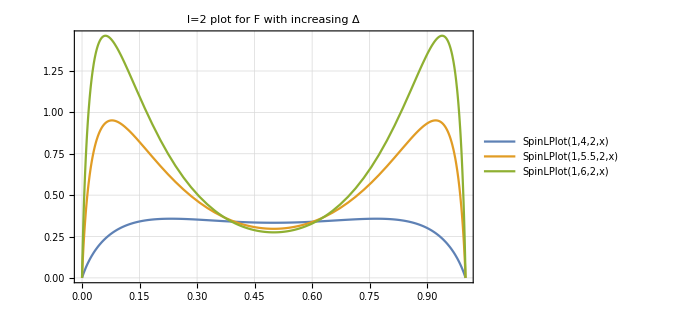

```mathematica
Plot[{SpinLPlot[1,4,2,x],SpinLPlot[1,5.5,2,x],SpinLPlot[1,6,2,x]},{x,0,1},PlotRange->Full,PlotTheme->"Detailed",PlotLabel->"
l=2 plot for F with increasing Δ ",ImageSize->500]
```

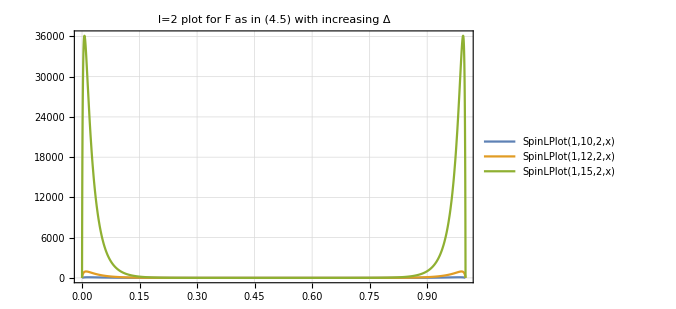

```mathematica
Plot[{SpinLPlot[1,10,2,x],SpinLPlot[1,12,2,x],SpinLPlot[1,15,2,x]},{x,0,1},PlotRange->Full,PlotTheme->"Detailed",PlotLabel->"
l=2 plot for F as in (4.5) with increasing Δ ",ImageSize->500]
```

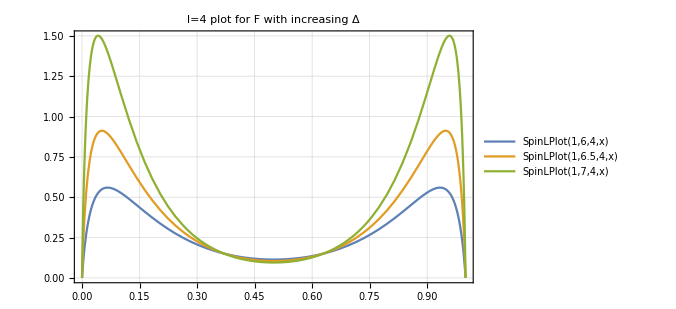

```mathematica
Plot[{SpinLPlot[1,6,4,x],SpinLPlot[1,6.5,4,x],SpinLPlot[1,7,4,x]},{x,0,1},PlotRange->Full,PlotTheme->"Detailed",PlotLabel->"
l=4 plot for F with increasing Δ ",ImageSize->500]
```

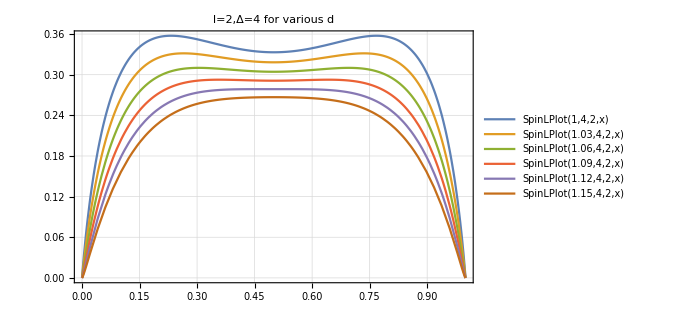

```mathematica
Plot[{SpinLPlot[1,4,2,x],SpinLPlot[1.03,4,2,x],SpinLPlot[1.06,4,2,x],SpinLPlot[1.09,4,2,x],SpinLPlot[1.12,4,2,x],SpinLPlot[1.15,4,2,x]},{x,0,1},PlotRange->Full,PlotTheme->"Detailed",PlotLabel->"l=2,Δ=4 for various d ",ImageSize->500]
```

Plot for various d shows that at d=1.12 the usual behaviour of the sum rule function remains the same.

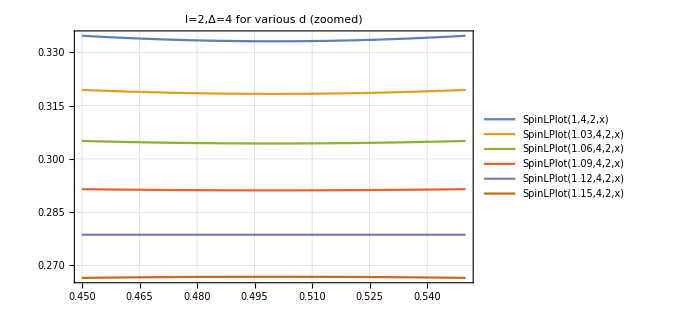

```mathematica
Plot[{SpinLPlot[1,4,2,x],SpinLPlot[1.03,4,2,x],SpinLPlot[1.06,4,2,x],SpinLPlot[1.09,4,2,x],SpinLPlot[1.12,4,2,x],SpinLPlot[1.15,4,2,x]},{x,0.45,0.55},PlotRange->Full,PlotTheme->"Detailed",PlotLabel->"l=2,Δ=4 for various d (zoomed) ",ImageSize->500]
```

“We have to determine if, for a given ∆min, the above system has a solution or not. It turns out that in the range d ≥ 1 and ∆min ≥ 2 which is of interest for us, all Fd,(0∆,0),l > 0 in the RHS of the inhomogeneous equation (5.4). In such a situation, if a nontrivial solution of the homogeneous system (5.5) is found, a solution of the full system (5.4), (5.5) can be obtained by a simple rescaling.Thus for our purposes it is enough to focus on the existence of nontrivial solutions of the homogeneous system (5.5)”

```mathematica
func[a_,b_,Δ_,l_]:=F[1,Δ,l,z,zb]/.{z->0.5+a+b,zb->0.5+a-b};
```

```mathematica
h=0.001;
f2a[Δ_,l_]:=((func[a+h,b,Δ,l]+func[a-h,b,Δ,l]-2*func[a,b,Δ,l])/h^2)/.{a->0.0001,b->0.0001}
f2b[Δ_,l_]:=((func[a,b+h,Δ,l]+func[a,b-h,Δ,l]-2*func[a,b,Δ,l])/h^2)/.{a->0.0001,b->0.0001}
```

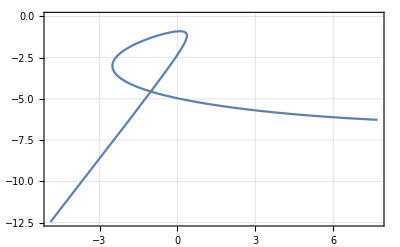

```mathematica
p1=ListLinePlot[Table[{f2a[Δ,0],f2b[Δ,0]},{Δ,1.01,5,0.01}],PlotTheme->"Detailed"]
```

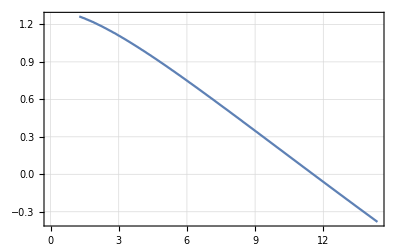

```mathematica
p2=ListLinePlot[Table[{f2a[Δ,2],f2b[Δ,2]},{Δ,4,7,0.01}],PlotTheme->"Detailed"]
```

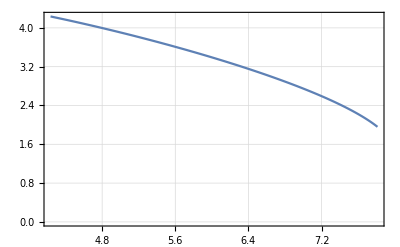

```mathematica
p3=ListLinePlot[Table[{f2a[Δ,4],f2b[Δ,4]},{Δ,6,9,0.01}],PlotTheme->"Detailed"]
```

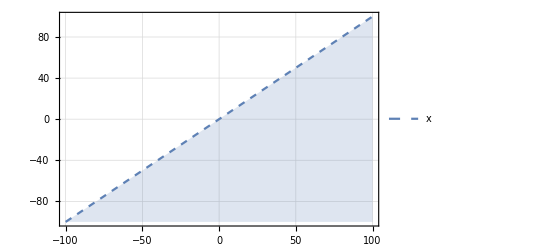

```mathematica
p4=Plot[x,{x,-100,100},Filling->Bottom,PlotTheme->"Detailed",PlotStyle->Dashed]
```

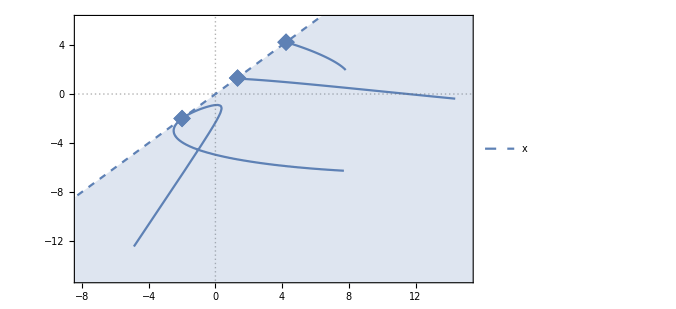

```mathematica
Show[p1,p2,p3,p4,ListPlot[{{f2a[2,0],f2b[2,0]}},PlotMarkers->{"◆", 18}],ListPlot[{{f2a[4,2],f2b[4,2]}},PlotMarkers->{"◆", 18}],ListPlot[{{f2a[6.0,4],f2b[6.0,4]}},PlotMarkers->{"◆", 18}],GridLines->{{0},{0}},PlotRange->{{-8,15},{-15,6}},ImageSize->500]
```

We plot the same graph but for d=1.05.

```mathematica
func2[a_,b_,Δ_,l_]:=F[1.05,Δ,l,z,zb]/.{z->0.5+a+b,zb->0.5+a-b};
```

```mathematica
f2a2[Δ_,l_]:=((func2[a+h,b,Δ,l]+func2[a-h,b,Δ,l]-2*func2[a,b,Δ,l])/h^2)/.{a->0.0001,b->0.0001}
f2b2[Δ_,l_]:=((func2[a,b+h,Δ,l]+func2[a,b-h,Δ,l]-2*func2[a,b,Δ,l])/h^2)/.{a->0.0001,b->0.0001}
```

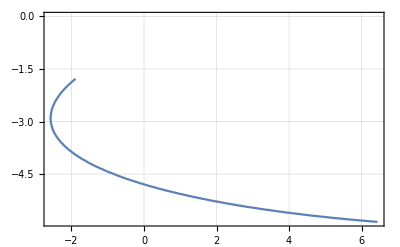

```mathematica
q1=ListLinePlot[Table[{f2a2[Δ,0],f2b2[Δ,0]},{Δ,2,5,0.01}],PlotTheme->"Detailed"]
```

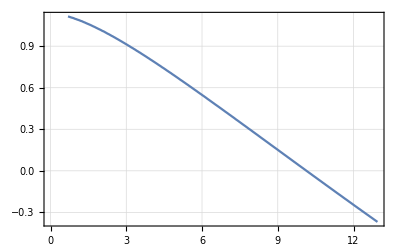

```mathematica
q2=ListLinePlot[Table[{f2a2[Δ,2],f2b2[Δ,2]},{Δ,4,7,0.01}],PlotTheme->"Detailed"]
```

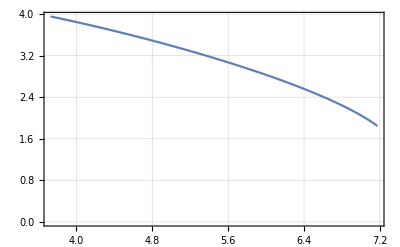

```mathematica
q3=ListLinePlot[Table[{f2a2[Δ,4],f2b2[Δ,4]},{Δ,6,9,0.01}],PlotTheme->"Detailed"]
```

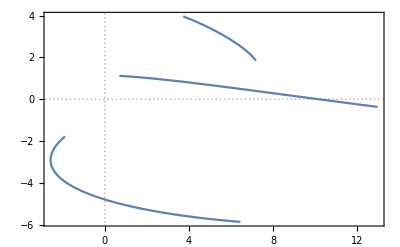

```mathematica
Show[q1,q2,q3,PlotRange->All,GridLines->{{0},{0}}]
```